# cascade lock diagnostics

## active adder transfer function

this data was taken using a rigol oscilloscope/function generator to supply a sine wave to input 2 on the adder, and both input and output were compared on a scope.  After making a measurement with the network analyzer, I am convinced that this is not representative of the adder, but may be indicative that the source impedance was frequency-dependent.

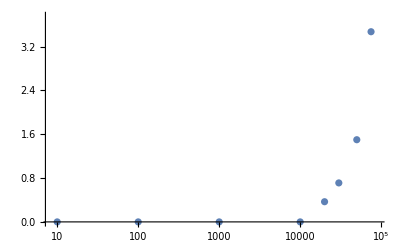

```mathematica
freq = {10,100,1000,10000,20000,30000,50000,75000, 90000};
gain = {1.085,1.085,1.085,1.085,1.132,1.1776,1.2895,1.618,2}/1.085;
data = Transpose@{freq,20Log10[gain]};
ListLogLinearPlot[data]
```

```mathematica
1.618/1.085
```

1.49124

## circuit to flatten the error gain

split error into two frequency bands, attenuate each band as needed, then recombine.

```mathematica
highG[ω_]:=(ω R1 C1)/(√(1+(ω R1 C1)^2));
lowG[ω_]:=1/(√(1+(ω L2/R2)^2));
Ceff = .5*8.2*^-8;
Leff = 2 L;
GLC[ω_]:=(ω Leff)/(√(1-Leff Ceff ω^2));
```

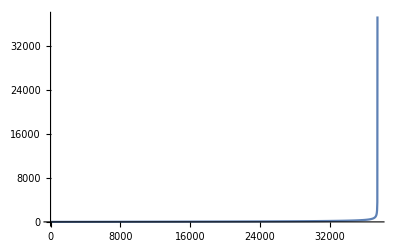

```mathematica
Plot[GLC[2π f],{f,0,100000},PlotRange->All]
```

```mathematica
GLC[0]
```

0.